```mathematica
(* Send to the right directory if necessary *)
(* the main project directory sits one above this subproject directory, i.e. at the -2 position. *)
projectDirectory=FileNameTake[NotebookDirectory[],{1,-2}]
packageDirectory=FileNameJoin@{projectDirectory,"mathematica_packages\\"}
outputDirectory=FileNameJoin@{projectDirectory,"output\\"}

If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]

Get["SMThreeChipModel.m"]
Get["SMThreeTraps.m"]
```

C:\Users\josep\forschung\modeling\bubble_bec

C:\Users\josep\forschung\modeling\bubble_bec\mathematica_packages

C:\Users\josep\forschung\modeling\bubble_bec\output

```mathematica
bFieldTOY[b0_,bCurve_,x_,y_,z_]:=b0+bCurve*{x^2,y^2,z^2};
(*bFieldMagTOY[b0_,bCurve_,x_,y_,z_]:=b0+bCurve*Sqrt[x^4+y^4+z^4];*)
bFieldMagTOY[b0_,bCurve_,x_,y_,z_]:=b0+bCurve*(x^2+(y/1.5)^2+z^2);

b0TOY=5*Gauss;(* G *)
bCurveTOY=1.5*10^(4);

hamiltonianTOY[Δ_,Ω_,x_,y_,z_]:=({{Δ,Ω/2,0},{Ω/2,0,Ω/2},{0,Ω/2,-Δ}}+{{#[[1]],0,0},{0,#[[3]],0},
{0,0,#[[5]]}}&[ZeemanShiftC@bFieldMagTOY[b0TOY,bCurveTOY,x,y,z]]);

adiabaticEnergiesTOY[Δ_,Ω_,x_,y_,z_]:=Eigenvalues@hamiltonianTOY[Δ,Ω,x,y,z];
adiabaticEnergyStatesTOY[Δ_,Ω_,x_,y_,z_]:=Eigenvectors@hamiltonianTOY[Δ,Ω,x,y,z];
maxAdiabaticEnergyTOY[Δ_,Ω_,x_,y_,z_]:=Max@Eigenvalues@hamiltonianTOY[Δ,Ω,x,y,z];
```

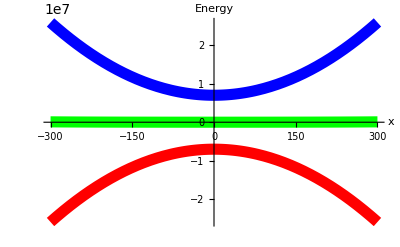

-Graphics3D-

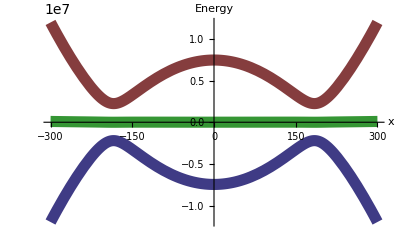
-Graphics- | -Graphics3D- | -Graphics-

```mathematica
energySplitting=(ZeemanShift[b0TOY]//Differences)[[4]];
cDelta=4*energySplitting+150*^3;
cOmega=(*1000*)500*(2*Pi)*1*^3;
xMax=300(**10^(-6)*); (* um *)
xMin=-xMax;
xStp=(xMax-xMin)/200;

defaultPlotOptions=Options[Plot];

myPlotOptions={
ColorFunctionScaling->False, (* Necessary for our user-defined functions for the plots' line colors to work. *)
(* Aesthetics: *)
PlotStyle->Thickness[0.02],
PlotRange->All,
AxesOrigin->{0,0},
AxesStyle->Thickness[0.01],
AxesLabel->{Automatic,"Energy"},
Ticks->None
};

SetOptions[Plot,myPlotOptions];

Block[
{energies,
curveColors=RGBColor/@{{1,0,0},{0,1,0},{0,0,1}}(*These triplets define the RGB colors for each of the bare states, -1 (red), 0 (green), and 1 (blue), respectively.*),
plot, legend
},

energies[x_]:=ZeemanShiftC[bFieldMagTOY[b0TOY,bCurveTOY,x*10^(-6),0,0]][[{1,3,5}]];

plot=Show[
Plot[energies[x][[#]],{x,xMin,xMax},ColorFunction->Function[{x,y},curveColors[[#]]]]&
/@{1,2,3}
];

legend=LineLegend[Reverse@curveColors,{"1","0","-1"}];

(*energiesBarePlot=Legended[plot,legend];*)
energiesBarePlot=plot
]

Block[
{energies,stateCompositionX,lineColorFunc,plot,legend},

energies[x_]:=adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0];
(* n=1 for the highest energy (and for us most interesting) eigenstate. *)
stateCompositionX[x_,n_]:=adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[n]]^2;
lineColorFunc[x_,n_]:=(RGBColor@stateCompositionX[x,n]);

plot=Show[
Plot[energies[x][[#]],{x,xMin,xMax},
ColorFunction->Function[{x,y},lineColorFunc[x,#]]]&
/@{1,2,3}
];

legend=LineLegend[{Blue,Green,Red},{"1","0","-1"}];

energiesDressedPlot=plot;

Legended[plot,legend];
]

defaultContourPlot3DOptions=Options[ContourPlot3D];
myContourPlot3DOptions={
RegionFunction->Function[{x,y,z},x<0||y>0||z<0], (* creates cross-section *)
RegionBoundaryStyle->None,
Ticks->None,
(*Boxed->False,*)
(*AxesOrigin->{0,0,0},*)
(*AxesStyle->Thickness[0.01],*)
AxesLabel->{"x","y","z"}
};

SetOptions[ContourPlot3D,myContourPlot3DOptions];

Block[{sphere,maxBound=1},
sphere[x_,y_,z_]:=x^2+y^2+z^2;

spinLegend=ContourPlot3D[
{sphere[x,y,z]==1(*,sphere[x,y,z]==3,sphere[x,y,z]==9*)},
{x,0,maxBound},{y,0,maxBound},{z,0,maxBound},
ColorFunction->Function[{x,y,z},RGBColor@{x,y,z}],
ContourStyle->Opacity[1],
Mesh->False,
BoxStyle->None,
AxesOrigin->{0,0,0},
AxesLabel->{"m=-1","m=0","m=1"},
Axes->True,
Boxed->False,
ViewPoint->({#,#,#}&[5]),
Lighting->{"Ambient",White}]
]

SetOptions[ContourPlot3D,defaultContourPlot3DOptions];

spinGrid=Grid@{{energiesBarePlot,spinLegend,energiesDressedPlot}}

SetOptions[Plot,defaultPlotOptions];
```

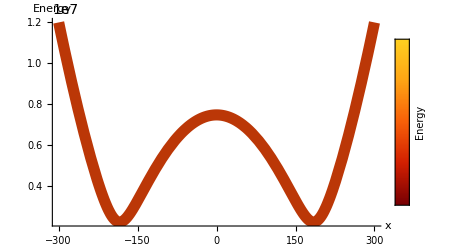

```mathematica
SetOptions[Plot,myPlotOptions];

plotPot1d=Legended[
Plot[adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]],{x,xMin,xMax},
ColorFunction->ColorData["SolarColors"],
ColorFunctionScaling->True,
Ticks->True],
BarLegend["SolarColors",Ticks->None,LegendLabel->"Energy"]
]

SetOptions[Plot,defaultPlotOptions];
```

```mathematica
ColorData["SolarColors"][0]
```

RGBColor[0.468742, 0., 0.0158236]

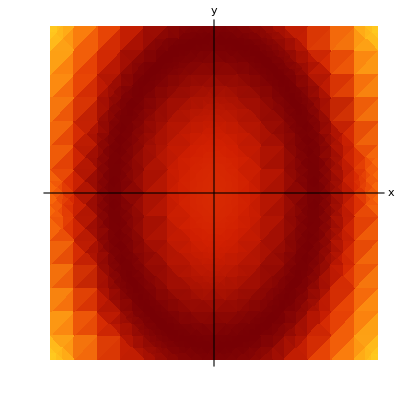

```mathematica
plotPot2d=DensityPlot[adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),0][[1]],
{x,xMin,xMax},{y,xMin,xMax},
ColorFunction->"SolarColors",
Frame->False,
Axes->True,
Ticks->False,
AxesStyle->Thickness[0.01],
AxesLabel->Automatic
]
```

3.2765×10^6

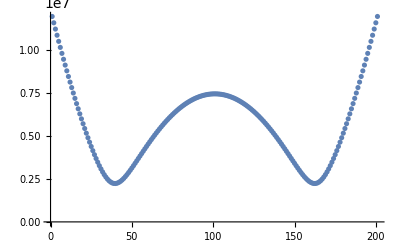

2.23797×10^6

-0.00018

```mathematica
roughMin=adiabaticEnergiesTOY[cDelta,cOmega,0.00015,0,0][[1]]
numEnergies=Table[adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]],{x,xMin,xMax,xStp}];
ListPlot@numEnergies
approxMin=Min@numEnergies
(minLoc=(Ordering[numEnergies,1][[1]]*xStp-300)*10^(-6))//N
```

```mathematica
(*Block[{energy,contourStyles,minEnergyOffset=0.15*^6,secondSurfaceOffset=5*^6},
energy[x_,y_,z_]:=(adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),z*10^(-6)][[1]]);

contourStyles=(Directive[ColorData["SolarColors"][#],Opacity[0.8]]&/@{0,1});

(*Print[contourStyles];*)

plotPot3d=ContourPlot3D[
{energy[x,y,z]==approxMin+minEnergyOffset,energy[x,y,z]==approxMin+secondSurfaceOffset},
{x,xMin,xMax},{y,xMin,xMax},{z,xMin,xMax},
(*PlotPoints->10,
MaxRecursion->4,*)
RegionFunction->Function[{x,y,z},x<0||y>0||z<0],
ContourStyle->{ColorData["SolarColors"][0],ColorData["SolarColors"][1]},
RegionBoundaryStyle->None]
]*)
```

```mathematica
Block[{energy,contourStyles,minEnergyOffset=0.15*^6,secondSurfaceOffset=5*^6},
energy[x_,y_,z_]:=(adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),z*10^(-6)][[1]]);

contourStyles=(Directive[ColorData["SolarColors"][#],Opacity[0.8]]&/@{0,1});

(*Print[contourStyles];*)

plotPot3dMin=ContourPlot3D[
energy[x,y,z]==approxMin+minEnergyOffset,
{x,xMin,xMax},{y,xMin,xMax},{z,xMin,xMax},
RegionFunction->Function[{x,y,z},(x<0||y>0||z<0)&&(x^2+(y/1.5)^2+z^2>(180^2))],
ContourStyle->ColorData["SolarColors"][0],
RegionBoundaryStyle->None]
]
```

CompiledFunction::cfsa: Argument 1/2000+15000. (x^2/1000000000000+4.44444×10^-13 y^2+z^2/1000000000000) at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

-Graphics3D-

```mathematica
Block[{energy,contourStyles,minEnergyOffset=0.15*^6,secondSurfaceOffset=4*^6},
energy[x_,y_,z_]:=(adiabaticEnergiesTOY[cDelta,cOmega,x*10^(-6),y*10^(-6),z*10^(-6)][[1]]);

contourStyles=(Directive[ColorData["SolarColors"][#],Opacity[0.8]]&/@{0,1});

(*Print[contourStyles];*)

plotPot3dOuter=ContourPlot3D[
energy[x,y,z]==approxMin+secondSurfaceOffset,
{x,xMin,xMax},{y,xMin,xMax},{z,xMin,xMax},
RegionFunction->Function[{x,y,z},x<0||y>0||z<0],
ContourStyle->ColorData["SolarColors"][0.8],
RegionBoundaryStyle->None]
]
```

CompiledFunction::cfsa: Argument 1/2000+15000. (x^2/1000000000000+4.44444×10^-13 y^2+z^2/1000000000000) at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

-Graphics3D-

```mathematica
plotPot3d=Show@{plotPot3dMin,plotPot3dOuter}
```

-Graphics3D-

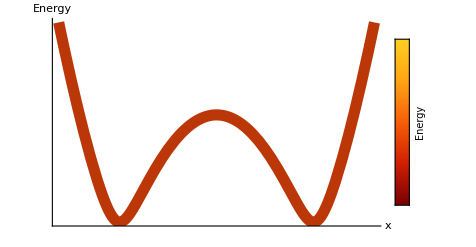
-Graphics- | -Graphics- | -Graphics3D-

```mathematica
energyGrid=Grid@{{
Show[plotPot1d,Ticks->False],
plotPot2d,
Show[plotPot3d,Ticks->False,AxesLabel->{"x","y","z"}]}}
```

```mathematica
Grid[{{spinGrid},{energyGrid}},Frame->All]
```

-Graphics- | -Graphics3D- | -Graphics-
-Graphics- | -Graphics- | -Graphics3D-

Dressing a bubble in a toy spin F=1 model. The spin dependent force experienced by atoms in a quadratic magnetic field is modified by the introduction of an rf field. The potential can be derived by transforming the atomic bare state atomic Hamiltonian into a rotating frame wherein time-dependence is removed by performing the rotating wave approximation. An atom whose introduction to and movement through the resulting potential is sufficiently adiabatic remains in one of the resulting energy curves.

By detuning the rf field from resonance at the minimum of the m=1 curve, potential dips are created at the points where the field is resonant. Any straight path that passes through the origin will experience the potential dips on either side of the B field minimum. Thus the minimum of the dressed potential forms a shell in dimensions.

Atoms with sufficiently low energy will be trapped around this minimum and form a bubble-shaped cloud.

```mathematica
SetOptions[ContourPlot3D,myContourPlot3DOptions];

Block[{sphere,plot1,plot2},
sphere[x_,y_,z_]:=x^2+y^2+z^2;
ContourPlot3D[{sphere[x,y,z]==1,sphere[x,y,z]==3,sphere[x,y,z]==9},
{x,-3,3},{y,-3,3},{z,-3,3},
(*RegionFunction->Function[{x,y,z},x<0||y>0||z<0],*)
ContourStyle->({#[1],#[0],#[1]}&[ColorData["SolarColors"]])];

plot1=ContourPlot3D[
{sphere[x,y,z]==1(*,sphere[x,y,z]==3,sphere[x,y,z]==9*)},
{x,-3,3},{y,-3,3},{z,-3,3},
RegionFunction->Function[{x,y,z},(x<0||y>0||z<0)&&(x^2+y^2+z^2<1.1)],
ContourStyle->({#[1],#[0],#[1]}&[ColorData["SolarColors"]])];

plot2=ContourPlot3D[{(*sphere[x,y,z]==1,*)sphere[x,y,z]==3(*,sphere[x,y,z]==9*)},
{x,-3,3},{y,-3,3},{z,-3,3},
ContourStyle->({#[1],#[0],#[1]}&[ColorData["SolarColors"]])];

Show@{plot1,plot2}

]

SetOptions[ContourPlot3D,defaultContourPlot3DOptions];
```

-Graphics3D-

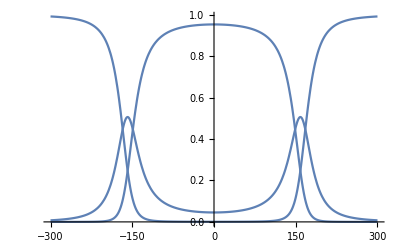

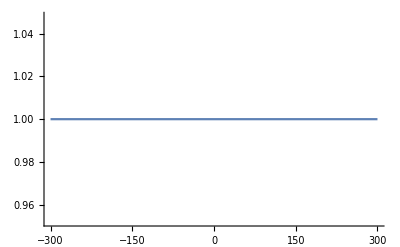

-Graphics3D-

```mathematica
Plot[adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]]^2,{x,xMin,xMax}]
Plot[Total@(#^2)&[adiabaticEnergyStatesTOY[cDelta,cOmega,x*10^(-6),0,0][[1]]],{x,xMin,xMax}]
```

```mathematica
Options[ContourPlot3D]
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→GrayLevel[0],Boxed→True,BoxRatios→{1,1,1},BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,Contours→Automatic,ContourStyle→GrayLevel[1],ControllerLinking→False,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,FaceGrids→None,FaceGridsStyle→{},FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#1&,#2&,#3&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionBoundaryStyle→Automatic,RegionFunction→(True&),RotationAction→Fit,SphericalRegion→Automatic,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},WorkingPrecision→MachinePrecision}